```mathematica
SetDirectory@FileNameJoin@{NotebookDirectory[],"..","data"}
```

```mathematica
Zip[a_List,b_List]:=Table[{a[[i]],b[[i]]},{i,1,Length[a]}]
Zip[a_List,b_List,c_List]:=Table[{a[[i]],b[[i]],c[[i]]},{i,1,Length[a]}]
Zip[a_List,b_List,c_List,d_List]:=Table[{a[[i]],b[[i]],c[[i]],d[[i]]},{i,1,Length[a]}]
```

```mathematica
Intersect[{a_,b_,c_},{p1_,p2_}]:=Module[{t,sol,line},line=(p1+(p2-p1)t ); sol=Solve[{a,b}.line==c,t];
tt=t/.sol;
If[Length[tt]>0 && tt[[1]]≥0 && tt[[1]] <1,line/. sol[[1]],{} ]
]
```

```mathematica
Intersect[{1,-1,1},{{0,0},{1,1}}]
```

{}

```mathematica
poly=Polygon[{{0,0},{1,0},{1,1},{0,1}}]
```

Polygon[{{0,0},{1,0},{1,1},{0,1}}]

```mathematica
Clear[rotate]
```

```mathematica
rotate[{x_,y_},phi_ : 0.0 , center_ : {0,0}]:= RotationMatrix[phi].({x,y}-center)+center
```

```mathematica
rotate[Polygon[p_List],phi_:0, center_ : {0,0}]:= Polygon[rotate[#,phi,center]&/@p]
```

```mathematica
Intersect[{a_,b_,c_},Polygon[ps_List]]:=
Module[{ins},ins=Partition[ps,2,1,{1,1}];
Select[Intersect[{a,b,c},#]&/@ins,Length[#]>0&]
]
```

```mathematica
eventToLine[{{x_,y_},phi_}]={Sin[phi],-Cos[phi],x Sin[phi] -y Cos[phi]}
```

{Sin[phi],-Cos[phi],-y Cos[phi]+x Sin[phi]}

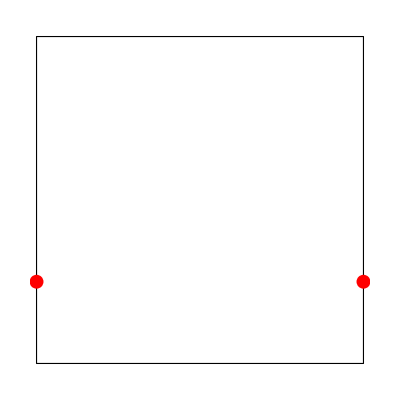

```mathematica
Graphics[{FaceForm[],EdgeForm[Black],poly,Red,PointSize[0.025],Point/@Intersect[{0,1,0.25},poly]}]
```

```mathematica
p1=rotate[Polygon[{{0.25,0.25},{0.5,0.25},{0.5,0.75},{0.25,0.75}}],-Pi/6,{0.25,0.25}]
```

Polygon[{{0.25,0.25},{0.466506,0.125},{0.716506,0.558013},{0.5,0.683013}}]

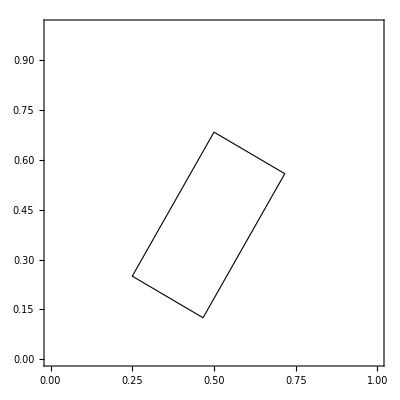

```mathematica
Graphics[{FaceForm[],EdgeForm[Black],p1},PlotRange->{{0,1},{0,1}},Frame->True]
```

```mathematica
nEvents= 500;
```

```mathematica
events=Table[{RandomReal[{0,1},2],RandomReal[2Pi]},{nEvents}];
```

```mathematica
lines= eventToLine/@events;
```

```mathematica
inters=Intersect[#,p1]&/@lines;
```

```mathematica
lengths=Length/@inters;
```

```mathematica
exp=Flatten/@Zip[events,lines,lengths,inters];
```

```mathematica
p1[[1]]
```

{{0.25,0.25},{0.466506,0.125},{0.716506,0.558013},{0.5,0.683013}}

```mathematica
out=OpenWrite["polygon.test"]
Write[out,nEvents]
Export[out,p1[[1]],"Table"]
Write[out]
Export[out,exp,"Table"]
Close[out]
"polygon.test"
```

OutputStream[polygon.test,31]

OutputStream[polygon.test,35]

OutputStream[polygon.test,31]

OutputStream[polygon.test,31]

polygon.test

polygon.test

```mathematica
Intersect[{a_,b_,c_},p_List]:=Module[{inters},inters=Intersect[{a,b,c},#]&/@p;{Position[inters,x_/;Length[x]>0,1], Select[inters,Length[#]>0 &]}]
```

```mathematica
h=0.020
w=0.006
r=0.450
nDetectors=280
```

0.02

0.006

0.45

280

```mathematica
scintilator=Polygon[{{r,-w/2},{r+h,-w/2},{r+h,w/2},{r,w/2}}]
```

Polygon[{{0.45,-0.003},{0.47,-0.003},{0.47,0.003},{0.45,0.003}}]

```mathematica
detector=Table[rotate[scintilator,i 2 Pi/nDetectors],{i,0,nDetectors-1}];
```

```mathematica
Intersect[{-1/Sqrt[2],1/Sqrt[2],0.2},detector]
```

{{{56},{156}},{{{0.157132,0.439975},{0.147354,0.430197}},{{-0.430197,-0.147354},{-0.439975,-0.157132}}}}

```mathematica
sdata=Select[Table[{RandomReal[{-r,r}/Sqrt[2],2],RandomReal[{-Pi,Pi}]},{1000}],(#[[1]].#[[1]]<1/2r^2)&];
```

```mathematica
lines=eventToLine/@sdata;
```

```mathematica
inters=Intersect[#,detector]&/@lines;
```

```mathematica
lengths=Length[#[[1]]]&/@inters;
```

```mathematica
exp=Flatten/@Zip[sdata,lengths,inters];
```

{0.224025,0.17467,0.119408,2,10,61,0.425852,0.198885,0.409289,0.196898,-0.453863,0.0933377,-0.460808,0.0925045}

```mathematica
out=OpenWrite["detector_ring.test"]
Export[out,{r,nDetectors,w,h,sdata//Length},"List"]
Write[out]
Export[out,exp,"Table"]
Close[out]
```

OutputStream[detector_ring.test,106]

OutputStream[detector_ring.test,106]

OutputStream[detector_ring.test,106]

detector_ring.test